### Plot out a few Legendre polynomials and observe the distribution of their roots

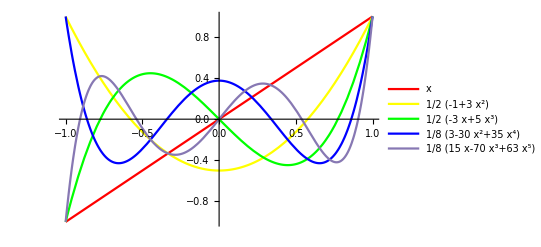

```mathematica
Plot[Evaluate[Table[LegendreP[n,x],{n,5}]],{x,-1,1},PlotStyle->{Red,Yellow,Green,Blue,Violet}, PlotLegends->"Expressions"]
```

### Observe that the distribution of roots gets denser towards the x=1 and -1

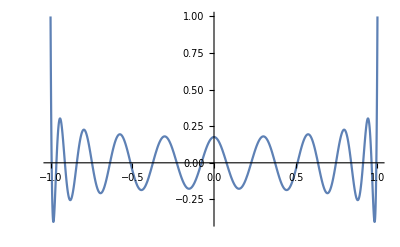

```mathematica
Plot[LegendreP[20,x],{x,-1,1}]
```

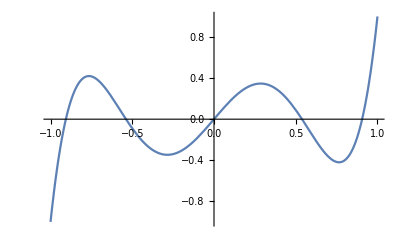

```mathematica
Plot[LegendreP[5,x],{x,-1,1}]
```

### Verify that Legendre Polynomial of degree 3, multiplied by f[x] will integrate to 0 in [-1,1] and will not be zero with g[x] (a polynomial of degree >3)

```mathematica
f[x_]:=x^2+10.0x-10
g[x_]:=x^5
```

```mathematica
Integrate[ f[x]LegendreP[3,x],{x,-1,1}]
```

0.

```mathematica
Integrate[ g[x]LegendreP[3,x],{x,-1,1}]
```

8/63